```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Block[
{f,r,l},
f[r_,l_]:=1+r^2/l^2;
EulerEquations[-Sqrt[r'[t]^2/f[r[t],l]-f[r[t],l]],r[t],t]
]
```

(-2 l^2 r[t]^3-r[t]^5+l^4 r[t] (-1+3 r'[t]^2)-l^6 r''[t]-l^4 r[t]^2 r''[t])/(l^2 √(-1-r[t]^2/l^2+(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0

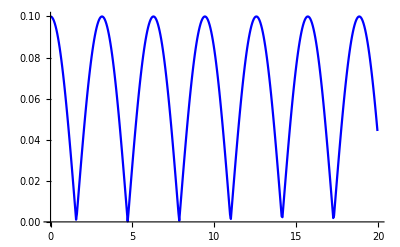

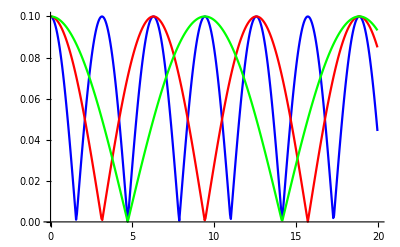

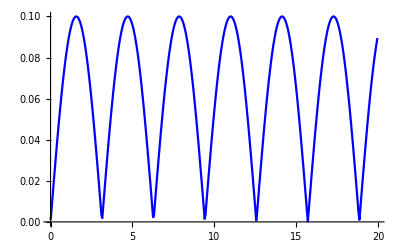

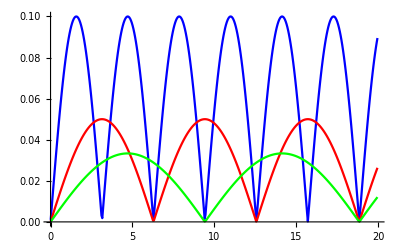

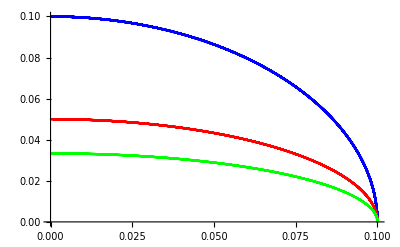

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(-2 l^2 r[t]^3-r[t]^5+l^4 r[t] (-1+3 r'[t]^2)-l^6 r''[t]-l^4 r[t]^2 r''[t])/(l^2 √(-1-r[t]^2/l^2+(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]-f[fr[l1,r1,t1],l1]^3];
Print[Show[
ListLinePlot[Table[{i,Abs[fr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[fr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,Abs[fr[2,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fr[3,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Green],
AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[pr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[pr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,Abs[pr[2,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pr[3,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Green],
AxesOrigin->{0,0}
]];
Print[Show[
ListLinePlot[Table[{Abs[fr[1,0.1,i]],Abs[pr[1,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{Abs[fr[2,0.1,i]],Abs[pr[2,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Red],
ListLinePlot[Table[{Abs[fr[3,0.1,i]],Abs[pr[3,0.1,i]]},{i,0.01,20,0.05}],PlotStyle->Green],
AxesOrigin->{0,0}
]];
]
```

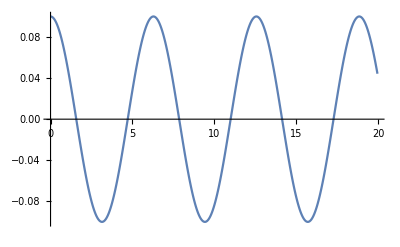

These are the values of pr against t, all of them pure imaginary.

{{0.01,0.+0.000995021 ⅈ},{0.06,0.+0.00596675 ⅈ},{0.11,0.+0.010924 ⅈ},{0.16,0.+0.0158548 ⅈ},{0.21,0.+0.0207471 ⅈ},{0.26,0.+0.0255889 ⅈ},{0.31,0.+0.0303686 ⅈ},{0.36,0.+0.0350744 ⅈ},{0.41,0.+0.0396946 ⅈ},{0.46,0.+0.044218 ⅈ},{0.51,0.+0.0486333 ⅈ},{0.56,0.+0.0529295 ⅈ},{0.61,0.+0.0570959 ⅈ},{0.66,0.+0.061122 ⅈ},{0.71,0.+0.0649975 ⅈ},{0.76,0.+0.0687127 ⅈ},{0.81,0.+0.072258 ⅈ},{0.86,0.+0.0756244 ⅈ},{0.91,0.+0.078803 ⅈ},{0.96,0.+0.0817856 ⅈ},{1.01,0.+0.0845645 ⅈ},{1.06,0.+0.0871323 ⅈ},{1.11,0.+0.0894821 ⅈ},{1.16,0.+0.0916079 ⅈ},{1.21,0.+0.0935038 ⅈ},{1.26,0.+0.0951649 ⅈ},{1.31,0.+0.0965867 ⅈ},{1.36,0.+0.0977653 ⅈ},{1.41,0.+0.0986975 ⅈ},{1.46,0.+0.0993808 ⅈ},{1.51,0.+0.0998134 ⅈ},{1.56,0.+0.0999941 ⅈ},{1.61,0.+0.0999224 ⅈ},{1.66,0.+0.0995985 ⅈ},{1.71,0.+0.0990232 ⅈ},{1.76,0.+0.0981982 ⅈ},{1.81,0.+0.0971257 ⅈ},{1.86,0.+0.0958085 ⅈ},{1.91,0.+0.0942503 ⅈ},{1.96,0.+0.0924552 ⅈ},{2.01,0.+0.090428 ⅈ},{2.06,0.+0.0881742 ⅈ},{2.11,0.+0.0856997 ⅈ},{2.16,0.+0.0830111 ⅈ},{2.21,0.+0.0801156 ⅈ},{2.26,0.+0.0770206 ⅈ},{2.31,0.+0.0737343 ⅈ},{2.36,0.+0.0702652 ⅈ},{2.41,0.+0.0666222 ⅈ},{2.46,0.+0.0628147 ⅈ},{2.51,0.+0.0588524 ⅈ},{2.56,0.+0.0547453 ⅈ},{2.61,0.+0.0505039 ⅈ},{2.66,0.+0.0461387 ⅈ},{2.71,0.+0.0416606 ⅈ},{2.76,0.+0.0370808 ⅈ},{2.81,0.+0.0324105 ⅈ},{2.86,0.+0.0276613 ⅈ},{2.91,0.+0.0228449 ⅈ},{2.96,0.+0.0179729 ⅈ},{3.01,0.+0.0130573 ⅈ},{3.06,0.+0.00811007 ⅈ},{3.11,0.+0.00314311 ⅈ},{3.16,0.-0.00183145 ⅈ},{3.21,0.-0.00680158 ⅈ},{3.26,0.-0.0117552 ⅈ},{3.31,0.-0.0166803 ⅈ},{3.36,0.-0.021565 ⅈ},{3.41,0.-0.0263972 ⅈ},{3.46,0.-0.0311653 ⅈ},{3.51,0.-0.0358574 ⅈ},{3.56,0.-0.0404622 ⅈ},{3.61,0.-0.0449682 ⅈ},{3.66,0.-0.0493642 ⅈ},{3.71,0.-0.0536394 ⅈ},{3.76,0.-0.0577829 ⅈ},{3.81,0.-0.0617844 ⅈ},{3.86,0.-0.0656337 ⅈ},{3.91,0.-0.069321 ⅈ},{3.96,0.-0.0728368 ⅈ},{4.01,0.-0.0761722 ⅈ},{4.06,0.-0.0793185 ⅈ},{4.11,0.-0.0822674 ⅈ},{4.16,0.-0.0850112 ⅈ},{4.21,0.-0.0875428 ⅈ},{4.26,0.-0.0898555 ⅈ},{4.31,0.-0.0919429 ⅈ},{4.36,0.-0.0937997 ⅈ},{4.41,0.-0.0954209 ⅈ},{4.46,0.-0.096802 ⅈ},{4.51,0.-0.0979393 ⅈ},{4.56,0.-0.0988299 ⅈ},{4.61,0.-0.0994712 ⅈ},{4.66,0.-0.0998615 ⅈ},{4.71,0.-0.0999998 ⅈ},{4.76,0.-0.0998856 ⅈ},{4.81,0.-0.0995193 ⅈ},{4.86,0.-0.098902 ⅈ},{4.91,0.-0.0980352 ⅈ},{4.96,0.-0.0969213 ⅈ},{5.01,0.-0.0955633 ⅈ},{5.06,0.-0.0939649 ⅈ},{5.11,0.-0.0921304 ⅈ},{5.16,0.-0.0900647 ⅈ},{5.21,0.-0.0877734 ⅈ},{5.26,0.-0.0852624 ⅈ},{5.31,0.-0.0825385 ⅈ},{5.36,0.-0.0796089 ⅈ},{5.41,0.-0.0764812 ⅈ},{5.46,0.-0.0731635 ⅈ},{5.51,0.-0.0696645 ⅈ},{5.56,0.-0.0659932 ⅈ},{5.61,0.-0.062159 ⅈ},{5.66,0.-0.0581716 ⅈ},{5.71,0.-0.0540412 ⅈ},{5.76,0.-0.0497782 ⅈ},{5.81,0.-0.0453933 ⅈ},{5.86,0.-0.0408973 ⅈ},{5.91,0.-0.0363015 ⅈ},{5.96,0.-0.0316172 ⅈ},{6.01,0.-0.0268559 ⅈ},{6.06,0.-0.0220293 ⅈ},{6.11,0.-0.0171491 ⅈ},{6.16,0.-0.0122274 ⅈ},{6.21,0.-0.00727593 ⅈ},{6.26,0.-0.00230687 ⅈ},{6.31,0.+0.0026678 ⅈ},{6.36,0.+0.00763602 ⅈ},{6.41,0.+0.0125857 ⅈ},{6.46,0.+0.0175048 ⅈ},{6.51,0.+0.0223815 ⅈ},{6.56,0.+0.0272037 ⅈ},{6.61,0.+0.0319598 ⅈ},{6.66,0.+0.0366382 ⅈ},{6.71,0.+0.0412271 ⅈ},{6.76,0.+0.0457154 ⅈ},{6.81,0.+0.0500919 ⅈ},{6.86,0.+0.0543456 ⅈ},{6.91,0.+0.0584659 ⅈ},{6.96,0.+0.0624426 ⅈ},{7.01,0.+0.0662653 ⅈ},{7.06,0.+0.0699244 ⅈ},{7.11,0.+0.0734105 ⅈ},{7.16,0.+0.0767147 ⅈ},{7.21,0.+0.0798283 ⅈ},{7.26,0.+0.0827433 ⅈ},{7.31,0.+0.085452 ⅈ},{7.36,0.+0.0879472 ⅈ},{7.41,0.+0.0902224 ⅈ},{7.46,0.+0.0922714 ⅈ},{7.51,0.+0.094089 ⅈ},{7.56,0.+0.09567 ⅈ},{7.61,0.+0.0970104 ⅈ},{7.66,0.+0.0981065 ⅈ},{7.71,0.+0.0989552 ⅈ},{7.76,0.+0.0995544 ⅈ},{7.81,0.+0.0999024 ⅈ},{7.86,0.+0.0999982 ⅈ},{7.91,0.+0.0998416 ⅈ},{7.96,0.+0.0994331 ⅈ},{8.01,0.+0.0987736 ⅈ},{8.06,0.+0.0978651 ⅈ},{8.11,0.+0.0967099 ⅈ},{8.16,0.+0.0953112 ⅈ},{8.21,0.+0.0936728 ⅈ},{8.26,0.+0.0917991 ⅈ},{8.31,0.+0.0896951 ⅈ},{8.36,0.+0.0873664 ⅈ},{8.41,0.+0.0848191 ⅈ},{8.46,0.+0.0820601 ⅈ},{8.51,0.+0.0790966 ⅈ},{8.56,0.+0.0759364 ⅈ},{8.61,0.+0.0725876 ⅈ},{8.66,0.+0.069059 ⅈ},{8.71,0.+0.0653596 ⅈ},{8.76,0.+0.0614989 ⅈ},{8.81,0.+0.0574868 ⅈ},{8.86,0.+0.0533334 ⅈ},{8.91,0.+0.0490491 ⅈ},{8.96,0.+0.0446448 ⅈ},{9.01,0.+0.0401312 ⅈ},{9.06,0.+0.0355197 ⅈ},{9.11,0.+0.0308217 ⅈ},{9.16,0.+0.0260486 ⅈ},{9.21,0.+0.0212121 ⅈ},{9.26,0.+0.0163241 ⅈ},{9.31,0.+0.0113966 ⅈ},{9.36,0.+0.00644132 ⅈ},{9.41,0.+0.00147046 ⅈ},{9.46,0.-0.00350398 ⅈ},{9.51,0.-0.00846988 ⅈ},{9.56,0.-0.0134153 ⅈ},{9.61,0.-0.0183281 ⅈ},{9.66,0.-0.0231964 ⅈ},{9.71,0.-0.0280084 ⅈ},{9.76,0.-0.0327523 ⅈ},{9.81,0.-0.0374163 ⅈ},{9.86,0.-0.0419891 ⅈ},{9.91,0.-0.0464594 ⅈ},{9.96,0.-0.050816 ⅈ},{10.01,0.-0.055048 ⅈ},{10.06,0.-0.059145 ⅈ},{10.11,0.-0.0630964 ⅈ},{10.16,0.-0.0668922 ⅈ},{10.21,0.-0.0705229 ⅈ},{10.26,0.-0.0739791 ⅈ},{10.31,0.-0.0772518 ⅈ},{10.36,0.-0.0803326 ⅈ},{10.41,0.-0.0832134 ⅈ},{10.46,0.-0.0858866 ⅈ},{10.51,0.-0.0883453 ⅈ},{10.56,0.-0.0905829 ⅈ},{10.61,0.-0.0925934 ⅈ},{10.66,0.-0.0943715 ⅈ},{10.71,0.-0.0959123 ⅈ},{10.76,0.-0.0972119 ⅈ},{10.81,0.-0.0982665 ⅈ},{10.86,0.-0.0990735 ⅈ},{10.91,0.-0.0996305 ⅈ},{10.96,0.-0.0999362 ⅈ},{11.01,0.-0.0999895 ⅈ},{11.06,0.-0.0997906 ⅈ},{11.11,0.-0.0993397 ⅈ},{11.16,0.-0.0986382 ⅈ},{11.21,0.-0.097688 ⅈ},{11.26,0.-0.0964917 ⅈ},{11.31,0.-0.0950524 ⅈ},{11.36,0.-0.0933741 ⅈ},{11.41,0.-0.0914613 ⅈ},{11.46,0.-0.0893191 ⅈ},{11.51,0.-0.0869532 ⅈ},{11.56,0.-0.0843698 ⅈ},{11.61,0.-0.0815759 ⅈ},{11.66,0.-0.0785788 ⅈ},{11.71,0.-0.0753862 ⅈ},{11.76,0.-0.0720066 ⅈ},{11.81,0.-0.0684486 ⅈ},{11.86,0.-0.0647215 ⅈ},{11.91,0.-0.0608347 ⅈ},{11.96,0.-0.0567981 ⅈ},{12.01,0.-0.0526219 ⅈ},{12.06,0.-0.0483167 ⅈ},{12.11,0.-0.0438932 ⅈ},{12.16,0.-0.0393623 ⅈ},{12.21,0.-0.0347355 ⅈ},{12.26,0.-0.030024 ⅈ},{12.31,0.-0.0252394 ⅈ},{12.36,0.-0.0203935 ⅈ},{12.41,0.-0.015498 ⅈ},{12.46,0.-0.010565 ⅈ},{12.51,0.-0.00560625 ⅈ},{12.56,0.-0.000633938 ⅈ},{12.61,0.+0.00433988 ⅈ},{12.66,0.+0.00930321 ⅈ},{12.71,0.+0.014244 ⅈ},{12.76,0.+0.0191501 ⅈ},{12.81,0.+0.0240098 ⅈ},{12.86,0.+0.0288112 ⅈ},{12.91,0.+0.0335424 ⅈ},{12.96,0.+0.0381919 ⅈ},{13.01,0.+0.0427483 ⅈ},{13.06,0.+0.0472002 ⅈ},{13.11,0.+0.0515366 ⅈ},{13.16,0.+0.0557467 ⅈ},{13.21,0.+0.0598198 ⅈ},{13.26,0.+0.0637458 ⅈ},{13.31,0.+0.0675146 ⅈ},{13.36,0.+0.0711165 ⅈ},{13.41,0.+0.0745424 ⅈ},{13.46,0.+0.0777835 ⅈ},{13.51,0.+0.0808312 ⅈ},{13.56,0.+0.0836776 ⅈ},{13.61,0.+0.0863153 ⅈ},{13.66,0.+0.0887372 ⅈ},{13.71,0.+0.090937 ⅈ},{13.76,0.+0.0929088 ⅈ},{13.81,0.+0.0946473 ⅈ},{13.86,0.+0.0961479 ⅈ},{13.91,0.+0.0974064 ⅈ},{13.96,0.+0.0984196 ⅈ},{14.01,0.+0.0991847 ⅈ},{14.06,0.+0.0996995 ⅈ},{14.11,0.+0.0999628 ⅈ},{14.16,0.+0.0999738 ⅈ},{14.21,0.+0.0997323 ⅈ},{14.26,0.+0.0992392 ⅈ},{14.31,0.+0.0984958 ⅈ},{14.36,0.+0.097504 ⅈ},{14.41,0.+0.0962666 ⅈ},{14.46,0.+0.0947868 ⅈ},{14.51,0.+0.0930688 ⅈ},{14.56,0.+0.091117 ⅈ},{14.61,0.+0.0889367 ⅈ},{14.66,0.+0.0865338 ⅈ},{14.71,0.+0.0839146 ⅈ},{14.76,0.+0.081086 ⅈ},{14.81,0.+0.0780554 ⅈ},{14.86,0.+0.0748308 ⅈ},{14.91,0.+0.0714206 ⅈ},{14.96,0.+0.0678335 ⅈ},{15.01,0.+0.0640789 ⅈ},{15.06,0.+0.0601661 ⅈ},{15.11,0.+0.0561053 ⅈ},{15.16,0.+0.0519067 ⅈ},{15.21,0.+0.0475809 ⅈ},{15.26,0.+0.0431385 ⅈ},{15.31,0.+0.0385908 ⅈ},{15.36,0.+0.0339489 ⅈ},{15.41,0.+0.0292243 ⅈ},{15.46,0.+0.0244286 ⅈ},{15.51,0.+0.0195735 ⅈ},{15.56,0.+0.0146709 ⅈ},{15.61,0.+0.00973263 ⅈ},{15.66,0.+0.00477079 ⅈ},{15.71,0.-0.000202597 ⅈ},{15.76,0.-0.00517552 ⅈ},{15.81,0.-0.0101359 ⅈ},{15.86,0.-0.0150716 ⅈ},{15.91,0.-0.0199709 ⅈ},{15.96,0.-0.0248216 ⅈ},{16.01,0.-0.0296119 ⅈ},{16.06,0.-0.0343302 ⅈ},{16.11,0.-0.0389649 ⅈ},{16.16,0.-0.0435044 ⅈ},{16.21,0.-0.0479377 ⅈ},{16.26,0.-0.0522537 ⅈ},{16.31,0.-0.0564414 ⅈ},{16.36,0.-0.0604905 ⅈ},{16.41,0.-0.0643908 ⅈ},{16.46,0.-0.0681321 ⅈ},{16.51,0.-0.0717051 ⅈ},{16.56,0.-0.0751006 ⅈ},{16.61,0.-0.0783097 ⅈ},{16.66,0.-0.0813241 ⅈ},{16.71,0.-0.0841359 ⅈ},{16.76,0.-0.0867378 ⅈ},{16.81,0.-0.0891228 ⅈ},{16.86,0.-0.0912846 ⅈ},{16.91,0.-0.0932176 ⅈ},{16.96,0.-0.0949164 ⅈ},{17.01,0.-0.0963765 ⅈ},{17.06,0.-0.097594 ⅈ},{17.11,0.-0.0985657 ⅈ},{17.16,0.-0.0992888 ⅈ},{17.21,0.-0.0997614 ⅈ},{17.26,0.-0.0999823 ⅈ},{17.31,0.-0.0999508 ⅈ},{17.36,0.-0.099667 ⅈ},{17.41,0.-0.0991317 ⅈ},{17.46,0.-0.0983463 ⅈ},{17.51,0.-0.097313 ⅈ},{17.56,0.-0.0960346 ⅈ},{17.61,0.-0.0945145 ⅈ},{17.66,0.-0.0927568 ⅈ},{17.71,0.-0.0907662 ⅈ},{17.76,0.-0.0885481 ⅈ},{17.81,0.-0.0861084 ⅈ},{17.86,0.-0.0834534 ⅈ},{17.91,0.-0.0805903 ⅈ},{17.96,0.-0.0775266 ⅈ},{18.01,0.-0.0742702 ⅈ},{18.06,0.-0.0708296 ⅈ},{18.11,0.-0.0672137 ⅈ},{18.16,0.-0.0634317 ⅈ},{18.21,0.-0.0594934 ⅈ},{18.26,0.-0.0554087 ⅈ},{18.31,0.-0.051188 ⅈ},{18.36,0.-0.0468417 ⅈ},{18.41,0.-0.0423809 ⅈ},{18.46,0.-0.0378165 ⅈ},{18.51,0.-0.0331599 ⅈ},{18.56,0.-0.0284226 ⅈ},{18.61,0.-0.023616 ⅈ},{18.66,0.-0.0187521 ⅈ},{18.71,0.-0.0138427 ⅈ},{18.76,0.-0.00889964 ⅈ},{18.81,0.-0.00393503 ⅈ},{18.86,0.+0.00103915 ⅈ},{18.91,0.+0.0060108 ⅈ},{18.96,0.+0.0109678 ⅈ},{19.01,0.+0.0158983 ⅈ},{19.06,0.+0.0207902 ⅈ},{19.11,0.+0.0256316 ⅈ},{19.16,0.+0.0304106 ⅈ},{19.21,0.+0.0351157 ⅈ},{19.26,0.+0.0397351 ⅈ},{19.31,0.+0.0442576 ⅈ},{19.36,0.+0.048672 ⅈ},{19.41,0.+0.052967 ⅈ},{19.46,0.+0.0571322 ⅈ},{19.51,0.+0.061157 ⅈ},{19.56,0.+0.0650312 ⅈ},{19.61,0.+0.068745 ⅈ},{19.66,0.+0.0722888 ⅈ},{19.71,0.+0.0756535 ⅈ},{19.76,0.+0.0788304 ⅈ},{19.81,0.+0.0818113 ⅈ},{19.86,0.+0.0845883 ⅈ},{19.91,0.+0.0871541 ⅈ},{19.96,0.+0.0895021 ⅈ}}

This is the plot of Im[pr] against t.

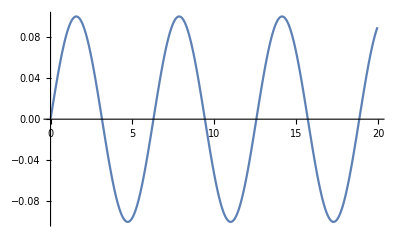

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_]:=NDSolveValue[{(-2 l^2 r[t]^3-r[t]^5+l^4 r[t] (-1+3 r'[t]^2)-l^6 r''[t]-l^4 r[t]^2 r''[t])/(l^2 √(-1-r[t]^2/l^2+(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0/.{l->l1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
fr[l1_,r1_,t1_]:=rm[l1,r1][t1];
dr[l1_,r1_,t1_]:=D[rm[l1,r1][t],t]/.{t->t1};
pr[l1_,r1_,t1_]:=dr[l1,r1,t1]/Sqrt[dr[l1,r1,t1]^2f[fr[l1,r1,t1],l1]-f[fr[l1,r1,t1],l1]^3];
Print[ListLinePlot[Table[{i,fr[1,0.1,i]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
Print["These are the values of pr against t, all of them pure imaginary."];
Print[Table[{i,pr[1,0.1,i]},{i,0.01,20,0.05}]];
Print["This is the plot of Im[pr] against t."];
Print[ListLinePlot[Table[{i,Im[pr[1,0.1,i]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```